## Skolemization

## Code

```mathematica
AQVariables[f_] := Flatten[Cases[f, HoldPattern[ForAll[q_, _]] :> q, {0, Infinity}]]
EQVariables[f_] := Flatten[Cases[f, HoldPattern[Exists[q_, _]] :> q, {0, Infinity}]]
AllOcurrences[f_] := Cases[f, _ForAll | _Exists, {0, Infinity}]
FreeOcurrences[f_] := Complement[Cases[FullForm[f], _Symbol, Infinity], EQVariables[f], AQVariables[f]];
TotalVariables[f_] := Join[Reverse[EQVariables[f]], Reverse[AQVariables[f]]];
TVariables[f_] := Reverse[Map[First, AllOcurrences[f]]]
Quantifiers[f_] := {StringCases[ToString[FullForm[f]], ("ForAll" | "Exists")], Count[Position[FullForm[f], ForAll], _] + Count[Position[FullForm[f], Exists], _]}
NestFormulae[f_] := Flatten[Reverse[Cases[f, HoldPattern[_[_, q_]] :> q, {0, Infinity}]]]
NestVariables[f_] := Flatten[Reverse[Cases[f, HoldPattern[_[q_, _]] :> q, {0, Infinity}]]]
Step1[f_] := 
	If[FreeQ[f, ForAll], 
	f /. Thread[EQVariables[f] -> Table[Subscript[c, n], {n, Count[EQVariables[f], _]}]], 
	f /. Thread[
		NestVariables[f][[
			1 ;; 
			Flatten[Position[Reverse[Map[Head, Cases[FullForm[f], _ForAll | _Exists, 
			{0, Infinity}]]], ForAll]][[1]] - 1]] -> 
				Table[Subscript[c, n], 
				{n, Flatten[Position[Reverse[Map[Head, Cases[FullForm[f], _ForAll | _Exists, 
					{0, Infinity}]]], ForAll]][[1]] - 1}]], f]
StepN[f_] := Nest[Step1, f, Count[Cases[f, _ForAll | _Exists, {0, Infinity}], _] + 1]
SkolemFunctions[fr_] := 
	Thread[
		EQVariables[fr] -> Table[Apply[Subscript[f, n], 
		Reverse[Table[Reverse[AQVariables[fr]][[1 ;; n]], 
		{n, Map[Length, Table[Cases[Map[Head, Reverse[Cases[Level[fr, {0, Infinity}],
			 _Exists | _ForAll]][[1 ;; n]]], ForAll], 
			 {n, Flatten[Position[Map[Head, Reverse[Cases[Level[fr, {0, Infinity}], 
				 _Exists | _ForAll]]], Exists]]}] ]}]][[n]]], {n, Length[EQVariables[fr]]}]]
skolemize[formula_] := StepN[formula] /. SkolemFunctions[formula] //. HoldPattern[Exists[_, q_]] :> q
```

## Tests

```mathematica
formula1= ForAll[x,Exists[y,ForAll[w,Exists[z, (R[x,y] ∨ ¬R[x,z] ∨ Q[y,w,z])]]]]
```

```mathematica
skolemize[formula1]
```

## Prenex Normal Form

```mathematica
eliminatEqiv[formula_]:=Block[{Equivalent=And[Implies[#1,#2],Implies[#2,#1]]&},formula];
```

```mathematica
eliminateImplies[formula_]:=Block[{Implies=Or[Not[#1],#2]&},formula];
```

```mathematica
standardizeVariables[And[f1_,f2_], n_, fixed_] := 
	Module[{sf1 ,sf2},
	sf1 = standardizeVariables[f1, n, fixed];
	sf2 = standardizeVariables[f2, sf1⟦2⟧, fixed];
	{And[First@sf1, First@sf2], sf2⟦2⟧ + 1 ,fixed}];
standardizeVariables[Or[f1_,f2_], n_, fixed_] := 
	Module[{sf1 ,sf2},
	sf1 = standardizeVariables[f1, n, fixed];
	sf2 = standardizeVariables[f2, sf1⟦2⟧, fixed];
	{Or[First@sf1, First@sf2], sf2⟦2⟧ + 1 ,fixed}];
standardizeVariables[HoldPattern[ForAll[x_,formula_]], n_, fixed_] := 
	If[MemberQ[fixed,x], 
		{ForAll[x, First@standardizeVariables[formula, n, fixed]], n, fixed},
		With[{sf = standardizeVariables[formula /. {x -> Subscript[x,n]}, n + 1, Append[fixed, Subscript[x,n]]]},
		{ForAll[Subscript[x,n], First@sf], sf⟦2⟧, fixed}]];
standardizeVariables[HoldPattern[Exists[x_,formula_]], n_, fixed_] := 
	If[MemberQ[fixed,x], 
		{Exists[x,First@standardizeVariables[formula, n, fixed]], n, fixed},
		With[{sf = standardizeVariables[formula /. {x -> Subscript[x,n]}, n + 1, Append[fixed, Subscript[x,n]]]},
		{Exists[Subscript[x,n], First@sf], sf⟦2⟧, fixed}]];
standardizeVariables[formula_, n_, fixed_] := {formula, n, fixed};
```

```mathematica
prefix[formula_] := Function[{expr, vars},Fold[#2[[1]][#2[[2]],#1]&, expr,
	Reverse[vars[[1]]]]]@@ Reap[Replace[formula, 
	(h:Verbatim[ForAll]|Verbatim[Exists])[var_, expr_] :> 
		(Sow[{Inactive[h],var}, "unwrap"];expr), {0, Infinity}],"unwrap"]//Activate;
```

```mathematica
prenexForm[formula_] := 
prefix@First@standardizeVariables[eliminateImplies@eliminatEqiv@formula,0,{}]
```

```mathematica
formula1 // FullForm
```

ForAll[x,Implies[ForAll[y,Implies[animal[y],loves[x,y]]],Exists[z,loves[z,x]]]]

```mathematica
formula1
```

∀_x(∀_y(animal[y]⇒loves[x,y])⇒∃_z loves[z,x])

```mathematica
skolemize@prenexForm[formula1]
```

∀_x_0(!(!animal[f_2[x_0]]||loves[x_0,f_2[x_0]])||loves[f_1[x_0],x_0])

## Most General Unifier

## Code

```mathematica
constants := {};
constantQ[term_] := MemberQ[constants, term];
variableQ[term_] := If[Depth[term] == 1 ∧ !MemberQ[constants, term],True,False];
unify[x_,y_] := 
Module[
	{iunify, result},
	iunify[s_?constantQ, t_?constantQ, sigma_] := If[s === t, sigma , Throw[$Failed]];
	iunify[f_[elems1___], g_[elems2___], sigma_] := 
		Module[
			{sigmaTemp = sigma},
			If[f === g ∧ Length[{elems1}] == Length[{elems2}],
				Do[
					sigmaTemp = Join[sigmaTemp, iunify[{elems1}⟦i⟧ //. sigmaTemp, {elems2}⟦i⟧ //.sigmaTemp , sigmaTemp] ]
					,{i, Range[Length@{elems1}]}
				];
				sigmaTemp,
				Throw[$Failed]
			]
		];
	iunify[s_?(Not@*variableQ), t_, sigma_] := iunify[t, s, sigma];
	iunify[s_,t_,sigma_] /; Count[t, s, {1, Infinity}] ≠ 0 := Throw[$Failed];
	iunify[s_,t_, sigma_] := Append[sigma, s-> t];
	result = Catch[iunify[x, y, {}]];
	If[MemberQ[result, $Failed] ∨ result === $Failed ∨ Not@DuplicateFreeQ[result,(First[#1]==First[#2]&&Last[#1]=!=Last[#2])&],
		$Failed, 
		result = Thread[Keys[result]->(Values[result]//.result)]; 
		DeleteDuplicates@result
		]
]
```

## Resolution

## Code

```mathematica
resolveLiteral[sLiteral_,tLiteral_] := If[unify[sLiteral,Not[tLiteral]] =!= $Failed, {sLiteral, tLiteral}, Null]; (*Returns pair of complementary literlas or Null*)
resolveClause[sClause_, tClause_] := DeleteCases[Flatten[Outer[resolveLiteral, sClause, tClause],1],Null]; (*Returns all pairs of complementary literals or Null*)
produceAllResolvents[sClause_, tClause_] := (* Returns a list of all resolvents of sClause and tClause i.e a list of lists *)
	Module[{literalPairs = resolveClause[sClause, tClause]},
		Map[Join[DeleteCases[sClause, #⟦1⟧], DeleteCases[tClause, #⟦2⟧]] /. unify[#⟦1⟧, Not[#⟦2⟧]]&, literalPairs]										 
	]

factor[clause_] := Module[{sigma, result = clause},
							Do[
								If[literal1 =!= literal2,
									sigma = unify[literal1, literal2];
									If[sigma =!= $Failed, result = Complement[clause, {literal2}] /. sigma; Break[], result = clause; Break[]],
								],
								{literal1, clause},{literal2, clause}
							];
							result
						]
factorAll[clause_] := DeleteDuplicates@FixedPoint[factor, clause];

resolve[sClause_, tClause_] := (*Returns a list of rules {sClause, tClause} -> resolvent for all resolvents of sClause and tClause i.e a specification of resolution graph for s and t*)
	Module[
		{kbTree = {}, resolvents = produceAllResolvents[sClause, tClause]},
		If[resolvents == {{}}, 
			kbTree = Append[kbTree, {sClause, tClause} -> "Contradiction!"],
		(*Else *)
			Do[
				kbTree = Append[kbTree, {sClause, tClause} ->  resolvent],
				{resolvent, resolvents}
			];
		];
		kbTree
	]

resolveAndFactor[sClause_, tClause_] := (*Returns a list of rules {sClause, tClause} -> resolvent for all resolvents of sClause and tClause i.e a specification of resolution graph for s and t*)
	Module[
		{kbTree = {}, resolvents = produceAllResolvents[sClause, tClause]},
		If[resolvents == {{}}, 
			kbTree = Append[kbTree, {sClause, tClause} -> "Contradiction!"],
		(*Else *)
			Do[
				kbTree = Append[kbTree, {sClause, tClause} ->  factorAll@resolvent],
				{resolvent, resolvents}
			];
		];
		kbTree
	]
	
chainToGraph[centralChain_, graph_] := 
	Module[
		{refined},
		refined = Select[graph, ((MemberQ[centralChain, #⟦1⟧⟦1⟧] ∨ MemberQ[centralChain, #⟦1⟧⟦2⟧]) ∧ MemberQ[centralChain, #⟦2⟧])&];
		Graph[Flatten[Map[{#⟦1⟧⟦1⟧ -> #⟦2⟧, #⟦1⟧⟦2⟧ -> #⟦2⟧}&, refined]], VertexLabels->"Name"]
	]

linearResolutionVerb[goal_, axioms_, k_] := 
	Module[{res, kbGraph = {}, centralChain},
		res["Contradiction!", ans_, n_] := Throw[Append[ans, "Contradiction!"]];
		res[clause_, ans_, 0] := Echo["Recursion Limit"];												
		res[clause_, ans_, n_] := Module[
								{resolventsRules},
								resolventsRules = Catenate[Echo[resolveAndFactor[Echo[clause, "C1 =  "], Echo[#, "C2 = "]], "resolveAndFactor = "]& /@ Union[ans, axioms]];
								kbGraph = Join[kbGraph, resolventsRules]; 
								res[#, Append[ans, clause], n - 1]& /@ Values[resolventsRules];
								];
		centralChain = Catch[res[goal, {}, k]];
		chainToGraph[centralChain, kbGraph]
	]

linearResolution[goal_, axioms_, k_] := 
	Module[{res, kbGraph = {}, centralChain, specialResolve},
		specialResolve[s_, t_] := specialResolve[s, t] = resolveAndFactor[s, t];
		res["Contradiction!", ans_, n_] := Throw[Append[ans, "Contradiction!"]];
		res[clause_, ans_, 0] := "Recursion Limit";												
		res[clause_, ans_, n_] := Module[
								{resolventsRules},
								resolventsRules = Catenate[specialResolve[clause,#]& /@ Union[ans, axioms]];
								kbGraph = Join[kbGraph, resolventsRules]; 
								res[#, Append[ans, clause], n - 1]& /@ Values[resolventsRules];
								];
		centralChain = Catch[res[goal, {}, k]];
		chainToGraph[centralChain, kbGraph]
	]		
		
				
resolution[goal_, kbInput_] := 
	Module[
	{support = {goal}, kbGraph = {}, kb = kbInput, newClauses, resolvents},
		NestWhile[
			(
			newClauses = {};
			Do[
				If[!MemberQ[Keys@kbGraph,{supportElem, kbElem}], 				
					kbGraph = Join[kbGraph, resolveAndFactor[supportElem, kbElem]];
					resolvents = produceAllResolvents[supportElem, kbElem];
					newClauses = Join[newClauses, resolvents];
					If[MemberQ[newClauses, {}], Break[]]
				],

				{supportElem, support},{kbElem, kb}
			];
			(* If[SubsetQ[kb, Echo[newClauses, "new = "] ], $Failed]; *)
			support = Union[support, newClauses];
			kb = Union[kb, newClauses];
			kbGraph)&,
			kbGraph,
			!MemberQ[kb, {}]&
			];
		kbGraph
	]	
	
makeGraph[assoc_] := Graph[Flatten[Map[{#⟦1⟧⟦1⟧ -> #⟦2⟧, #⟦1⟧⟦2⟧ -> #⟦2⟧}&, assoc]], VertexLabels->"Name"]
```

```mathematica
goal={!S[w]};
kb={{!G[x],H[x]},{!H[y],S[y]},{G[a]}};

goal1 = {!Cr[West[]]};
kb1 = {{!A[x],!W[y],!S[x,y,z],!H[z],Cr[x]},
		{!M[w], !Ow[Nono[],w], S[West[],w,Nono[]]},
		{!En[q,America[]],H[q]},
		{!M[r],W[r]},
		{Ow[Nono[], Rocket[]]},
		{A[West[]]},
		{M[Rocket[]]},
		{En[Nono[], America[]]}
};

goal2 = {!Ki[Curiosity[], Tuna[]]};
kb2 = {{A[F[x]], L[G[x],x]},
		{!L[y,F[y]], L[G[y],y]},
		{!L[q,w], A[z], !Ki[w,z]},
		{!A[r], L[Jack[], r]},
		{Ki[Jack[],Tuna[]], Ki[Curiosity[], Tuna[]]},
		{Ca[Tuna[]]},
		{!Ca[t], A[t]}};
		
goal3 = {!B[a]};
kb3 = {{!P[y],A[y],B[y]},
		{P[z]},
		{!A[w]}};
		
goal4 = {B[T]};
kb4 = {
		{W[T[]]},
		{!W[x], A[x]},
		{!B[x], !A[x]}
		};

goal5 = {p[x], l[x], Q[]};
kb5 = {
		{!p[B[]]},
		{!Q[], l[y]},
		{!l[z], r[z]},
		{!r[q], !l[t]} 
       };		

thm = {!eq[f[f[a[],b[]],f[c[],d[]]], f[f[d[],c[]],f[b[],a[]]]]};
axioms ={
			{eq[x,x]},
			{!eq[y,z], eq[z,y]},
			{!eq[p,q], !eq[q,r], eq[p,r]},
			{eq[f[i,j], f[j,i]]},
			{!eq[n,m],!eq[k,l],eq[f[n,k],f[m,l]]}
		};
```

## Tests:

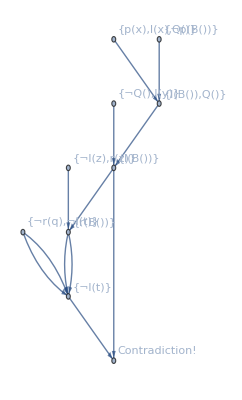

```mathematica
linearResolution[goal5, kb5 ,5]
```

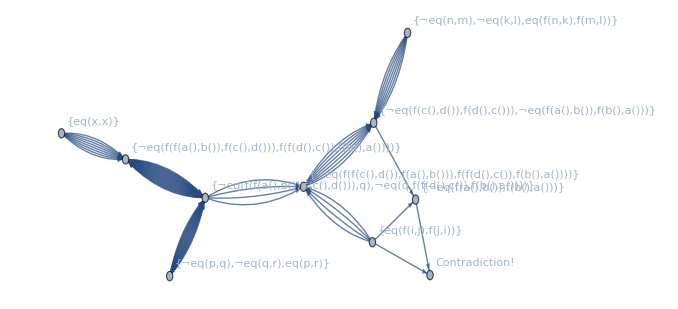

```mathematica
linearResolution[thm, axioms, 5]
```

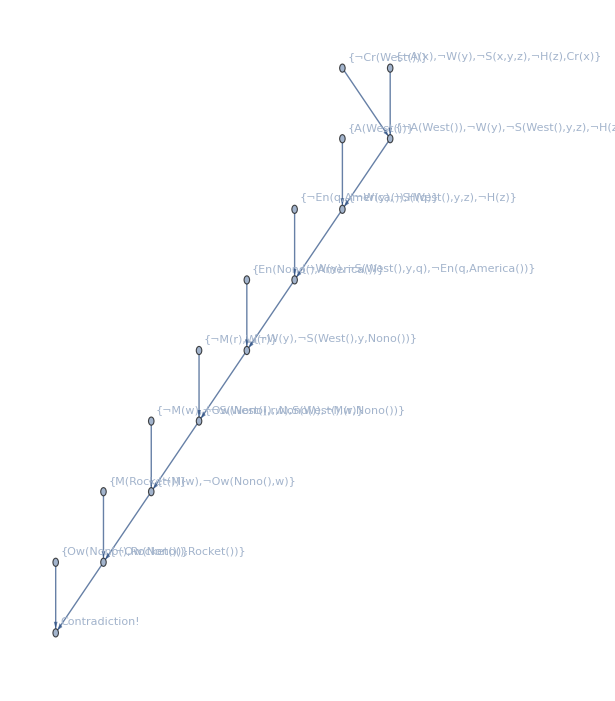

```mathematica
linearResolution[goal1,kb1,8]
```